```mathematica
image1 = Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\early_neural_network.png"];
image2 = Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\Bengio_Paper_Neural_Probabilistic_Language_Model.png"];
image3 = Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\advanced_neural_network.png"];
image4 = Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\word2vec_paper.png"];
image5=Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\openai_logo.png"];
image6=Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\seq2seq_model.png"];
image7=Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\attention.png"];
image8=Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\bert.png"];
image9=Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\attention_is_all_you_need.png"];
image10=Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\ug3p141_chatbot_robot_in_office_surroundings_realistic_photo_860241a0-daa3-4f06-accd-9210d6c8741e.png"];
image11=Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\Blog\\ug3p141.github.io\\assets\\huggingface_logo-noborder.svg"];
```

```mathematica
events=
{
{DateInterval[{DateObject[{1988}],DateObject[{1995}]}],image1,"NN Foundations",150},
{DateObject[{2001}],image2,"NN Language Model",150},
{DateObject[{2003}],image3,"Bengio, Improvements",150},
{DateObject[{2013}],image4,"Word2Vec",100},
{DateObject[{2014}],image6,"Seq2seq",150},
{DateObject[{2015}],image7,"Attention",150},
{DateObject[{2018}],image9,"Transformer",150},
{DateObject[{2018}],image8,"BERT",50},
{DateObject[{2019}],image5,"GPT-2",50},
{DateObject[{2020}],image5,"GPT-3",50},
{DateObject[{2021}],image10,"LLM Applications",50},
{DateObject[{2022}],image5,"GPT-3.5",50},
{DateObject[{2022}],image5,"ChatGPT",50},
{DateObject[{2023}],image11,"LLMs OSS",59}};
```

```mathematica
picturedevents=#1->Labeled[ImageResize[#2,#4],#3,Top]&@@@events;
```

```mathematica
TimelinePlot[picturedevents,PlotStyle->{Thick,PointSize[Large]},DateTicksFormat->{"Year"},FrameLabel->{None,None,"Year",None},PlotLabel->Style["Timeline of Large Language Models",Bold,32],AxesOrigin->Center,PlotLayout->"Grouped"]
```

-Graphics-

```mathematica
data=EntityValue[EntityClass["Movie","StarTrekFranchise"],{"ReleaseDate","Image","Name"}];

movieInfo=#1->Labeled[ImageResize[#2,40],#3,Right]&@@@data;
```

```mathematica
data
```

{{Fri 8 May 2009,-Graphics-,Star Trek},{Fri 22 Nov 1996,-Graphics-,Star Trek: First Contact},{Fri 18 Nov 1994,-Graphics-,Star Trek Generations},{Fri 11 Dec 1998,-Graphics-,Star Trek: Insurrection},{Fri 13 Dec 2002,-Graphics-,Star Trek: Nemesis},{Fri 7 Dec 1979,-Graphics-,Star Trek: The Motion Picture},{Fri 22 Jul 2016,-Graphics-,Star Trek Beyond},{Fri 4 Jun 1982,-Graphics-,Star Trek II: The Wrath of Khan},{Fri 1 Jun 1984,-Graphics-,Star Trek III: The Search for Spock},{Wed 26 Nov 1986,-Graphics-,Star Trek IV: The Voyage Home},{Thu 16 May 2013,-Graphics-,Star Trek Into Darkness},{Fri 9 Jun 1989,-Graphics-,Star Trek V: The Final Frontier},{Fri 6 Dec 1991,-Graphics-,Star Trek VI: The Undiscovered Country}}

```mathematica
TimelinePlot[movieInfo,AxesOrigin->Center,PlotLayout->"Grouped"]
```

-Graphics-

```mathematica
Clear[FormulaNeuralNetworkGraph]
FormulaNeuralNetworkGraph[layerCounts:{_Integer,_Integer,_Integer}]:=Block[{gr1,gr2,gr3,gr4,gr,bc},gr1=IndexGraph[CompleteGraph[Take[layerCounts,2]]];
gr2=Graph[Map[(layerCounts[[1]]+#)<->(layerCounts[[1]]+layerCounts[[2]]+#)&,Range[layerCounts[[2]]]]];
gr3=IndexGraph[CompleteGraph[Take[layerCounts,-2]],layerCounts[[1]]+layerCounts[[2]]+1];
bc=layerCounts[[1]]+2*layerCounts[[2]];
gr4=Graph[Map[(bc+#)<->(bc+layerCounts[[3]]+#)&,Range[layerCounts[[3]]]],VertexLabels->"Name"];
gr=GraphUnion[gr1,gr2,gr3,gr4];
Graph[gr,GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{layerCounts[[1]],layerCounts[[2]],layerCounts[[2]],layerCounts[[3]],layerCounts[[3]]}}]];

Clear[FormulaNeuralNetworkGraphPlot]
Options[FormulaNeuralNetworkGraphPlot]=Options[Graphics];

FormulaNeuralNetworkGraphPlot[layerCounts:{_Integer,_Integer,_Integer},func1_,opts:OptionsPattern[]]:=FormulaNeuralNetworkGraphPlot[layerCounts,func1,#&,opts];

FormulaNeuralNetworkGraphPlot[layerCounts:{_Integer,_Integer,_Integer},func1_,func2_,opts:OptionsPattern[]]:=Block[{plOpts,grFunc1,grFunc2,gr,vNames,vCoords,vNameToCoordsRules,edgeLines},plOpts={PlotTheme->"Default",Axes->True,Ticks->False,Frame->True,FrameTicks->False,ImageSize->Small};
grFunc1=Plot[func1[x],{x,-2,2},Evaluate[plOpts]];
grFunc2=Plot[func2[x],{x,-2,2},Evaluate[plOpts]];
gr=FormulaNeuralNetworkGraph[layerCounts];
vNames=VertexList[gr];
vCoords=VertexCoordinates/. AbsoluteOptions[gr,VertexCoordinates];
vNameToCoordsRules=Thread[vNames->vCoords];
edgeLines=Arrow@ReplaceAll[List@@@EdgeList[gr],vNameToCoordsRules];
Graphics[{Arrowheads[0.02],GrayLevel[0.2],edgeLines,EdgeForm[Black],FaceForm[Gray],Map[Disk[#,0.04]&,vCoords[[1;;-layerCounts[[-1]]-1]]],Black,Map[{EdgeForm[Gray],FaceForm[White],Disk[#,0.14],Text[Style["∑",16,Bold],#]}&,Join[vCoords[[layerCounts[[1]]+1;;layerCounts[[1]]+layerCounts[[2]]]],vCoords[[-2 layerCounts[[-1]];;-layerCounts[[-1]]-1]]]],Map[{EdgeForm[None],FaceForm[White],Rectangle[#-{0.2,0.15},#+{0.2,0.15}],Inset[grFunc1,#1,Center,0.4]}&,vCoords[[Total[layerCounts[[1;;2]]]+1;;Total[layerCounts[[1;;2]]]+layerCounts[[2]]]]],Map[{EdgeForm[None],FaceForm[White],Rectangle[#-{0.2,0.15},#+{0.2,0.15}],Inset[grFunc2,#1,Center,0.4]}&,MapThread[Mean@*List,{vCoords[[-2 layerCounts[[-1]];;-layerCounts[[-1]]-1]],vCoords[[-layerCounts[[-1]];;-1]]}]]},opts]];
```

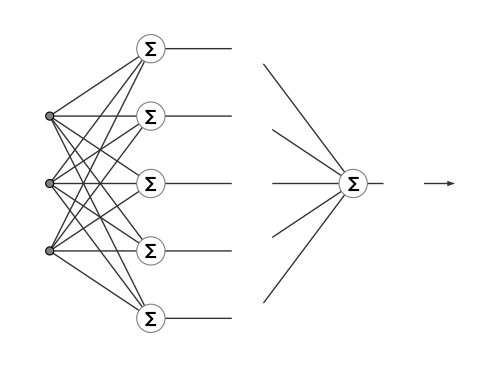
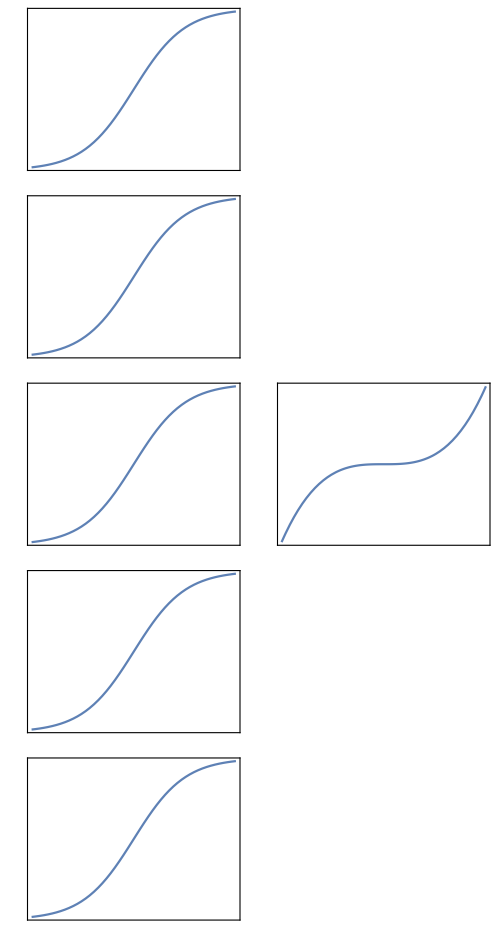

```mathematica
FormulaNeuralNetworkGraphPlot[{3,5,1},Tanh,#^3&,ImageSize->500]
```

```mathematica
ClearAll[layeredNW]
layeredNW[layers:{__},opts:OptionsPattern[Graph]]:=Module[{cg=CompleteGraph[layers,DirectedEdges->True]},SetProperty[EdgeDelete[cg,DirectedEdge[a_,b_]/;(Subtract@@(PropertyValue[{cg,#},VertexCoordinates][[1]]&/@{b,a})>1)],{PerformanceGoal->"Quality",VertexSize->.5,VertexStyle->White,EdgeStyle->Black,VertexCoordinates->GraphEmbedding[cg],opts}]]
```

```mathematica
layers={3,5,7,5,1};
colors=Flatten[MapThread[ConstantArray,{ColorData[63,"ColorList"][[;;Length@layers]],layers}]];
Show[layeredNW[layers,VertexStyle->{i_:>colors[[i]]},ImageSize->Large,VertexSize->.3],ImageSize->500]
```

-Graphics-

```mathematica
a1 = ArrayPlot[ConstantArray[1,{2,3}],ColorRules->{1->LightPurple},Mesh->True];
a2= ArrayPlot[ConstantArray[1,{3,2}],ColorRules->{1->LightOrange},Mesh->True];
a3= ArrayPlot[ConstantArray[1,{2,3}],ColorRules->{1->LightBlue},Mesh->True];
a4= ArrayPlot[ConstantArray[1,{2,3}],ColorRules->{1->LightPink},Mesh->True];
```

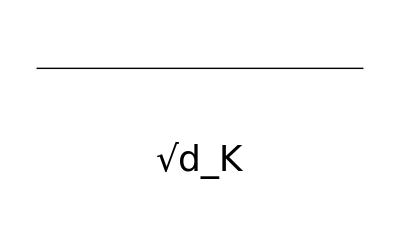

```mathematica
g1=GraphicsColumn[
{GraphicsRow[{Graphics[Text[Style["Q",36,Purple]]],Graphics[Text[Style["",36]]],Graphics[Text[Style["    K^T",36,Orange]]]}],
GraphicsRow[{a1,Graphics[Text[Style["×",36]]],a2},0],
Graphics[{Thick,Line[{{-6,0},{1,0}}]}],
Graphics[Text[Style["√d_K",36]]]
},
Alignment->Center,
Spacings->-50.]
```

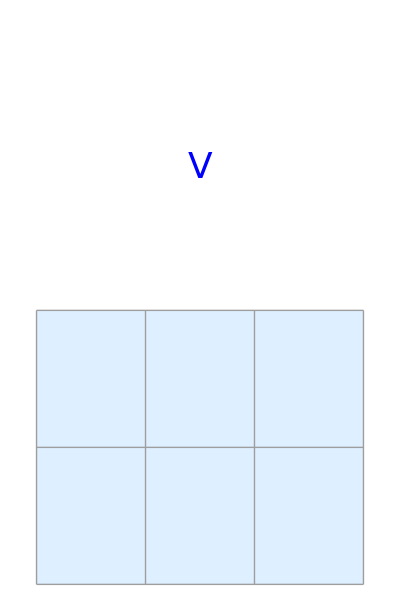

```mathematica
g2=GraphicsColumn[
{Graphics[Text[Style["V",36,Blue]]],
a3
},
Alignment->Center,
Spacings->-50.]
```

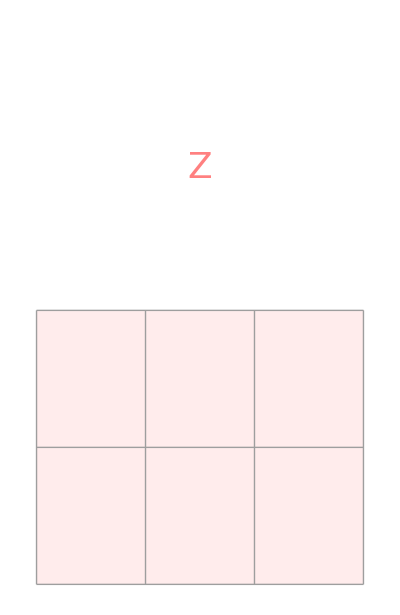

```mathematica
g3=GraphicsColumn[
{Graphics[Text[Style["Z",36,Pink]]],
a4
},
Alignment->Center,
Spacings->-50.]
```

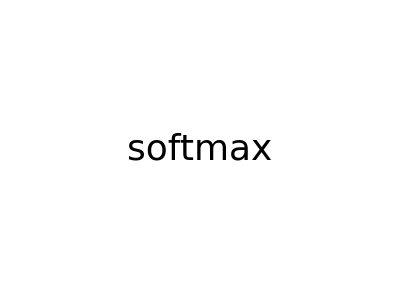
-Graphics- | ( | -Graphics- | ) | -Graphics- | = | -Graphics-

```mathematica
g4=Grid[
{{
Graphics[Text[Style["softmax",36,Black,Thick]]],
Text[Style["(",36,Thick]],
Image[g1,ImageSize->{200,200},BaselinePosition->Scaled[0.4]],
Text[Style[")",36,Thick]],
Image[g2,ImageSize->{150,150},BaselinePosition->Scaled[0.2]],
Text[Style["=",24,Thick]],
Image[g3,ImageSize->{150,150},BaselinePosition->Scaled[0.2]]
}},
Spacings->{0,0}
]
```